```mathematica
Needs["drawTx`"]
```

```mathematica
Needs["simulateTx`"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
RandExp[x_]:=-1/x*Log[Random[Real]];
```

```mathematica
ThAcum[lpkt_]:=Map[#[[3]]/(#[[1]]+#[[2]])&,lpkt]
```

```mathematica
OmnetThAcum[csv_]:=Map[(#[[2]]/#[[1]])&,csv]
```

```mathematica
speed = 1;
tp = 1;
ackT = 1;
lmb = 1;
mu = 10;
init = 0;
n = 1000;
p = 0.1;
```

```mathematica
SW = (SetInitPar[speed,tp,ackT];ToTime[FifoSW[GetPacketArrival[RandExp[1/lmb],RandExp[1/mu],init,n],p]]);
```

```mathematica
GBN = (SetInitPar[speed,tp,ackT];ToTime[FifoGBN[GetPacketArrival[RandExp[1/lmb],RandExp[1/mu],init,n],p]]);
```

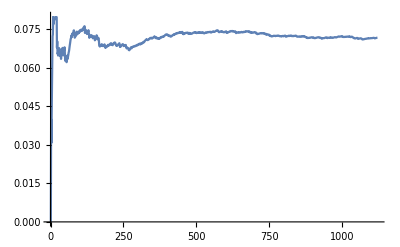

```mathematica
lSW=ListLinePlot[ThAcum[SW]]
```

```mathematica
Last[ThAcum[SW]]
```

0.0716588

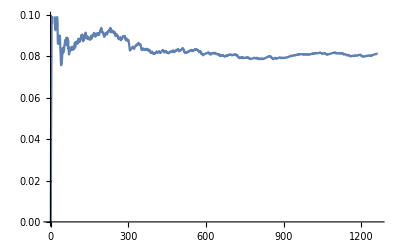

```mathematica
lGBN=ListLinePlot[ThAcum[GBN]]
```

```mathematica
GBNPktCnt=Import["GBN_rcvPktCount_1_1_1_exp_1_exp_10_10.csv","table",FieldSeparators->";"][[2;;All]];
```

```mathematica
oGBN  =OmnetThAcum[GBNPktCnt];
```

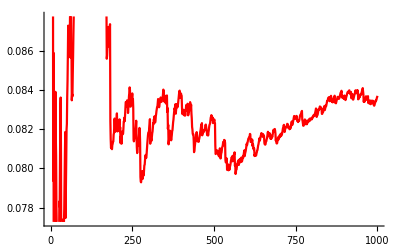

```mathematica
olGBN=ListLinePlot[oGBN,PlotStyle->Red]
```

```mathematica
Last[ThAcum[GBN]]
```

0.0811683

```mathematica
Last[oGBN]
```

0.0836904

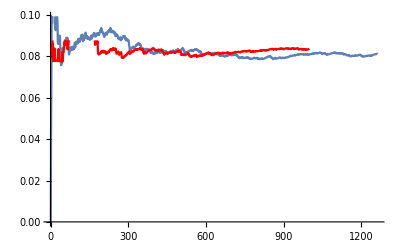

```mathematica
Show[lGBN,olGBN]
```

```mathematica
SWPktCnt=Import["SW_rcvPktCount_1_1_1_exp_1_exp_10_10.csv","table",FieldSeparators->";"][[2;;All]];
```

```mathematica
oSW =OmnetThAcum[SWPktCnt];
```

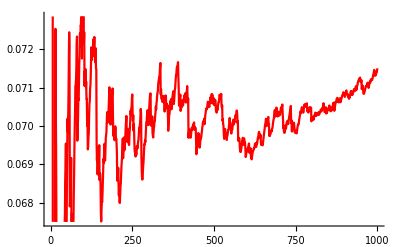

```mathematica
olSW=ListLinePlot[oSW,PlotStyle->Red]
```

```mathematica
Last[ThAcum[SW]]
```

0.0716588

```mathematica
Last[oSW]
```

0.0715062

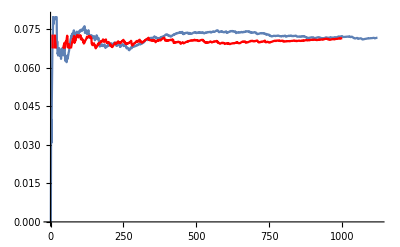

```mathematica
Show[lSW,olSW]
```